## Meta-settings

```mathematica
$Version
```

```mathematica
Charting`ResolvePlotTheme[Automatic,VectorPlot];
vcf=ColorDataFunction[…];
```

```mathematica
Monitor`NestList[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
(*WFQTransit[weights_List,relaxation_:0]:=Function[state,RandomChoice[weights:>((#+state)&/@(IdentityMatrix[Length]~Join~(-IdentityMatrix[Length[state]])))]]*)
```

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

### Test for Изжо Лю

```mathematica
n=4;
Normal@SparseArray[{{i_,j_}/;j>i:>ⅇ^(-ⅈ*π/4)},{n,n}];
mat=%+%†+IdentityMatrix[n];
Clear[n]
mat//MatrixForm
PositiveSemidefiniteMatrixQ@mat
```

## Soft transitter

### Basic Idea

```mathematica
ComplexPlot3D[(1+ⅇ^(-Im@z))(1-ⅇ^(-Re@z))+ⅈ(1+ⅇ^(-Re@z))(1-ⅇ^(-Im@z)),{z,0*(1+ ⅈ),2ⅇ*(1+ ⅈ)},ColorFunction->(Hue[2.95*(#8+0.5)]&),PlotLegends->BarLegend["Rainbow"],PlotRange->All,Mesh->Full]
```

```mathematica
Simplify[(1+ⅇ^(-Im@z))(1-ⅇ^(-Re@z))+ⅈ(1+ⅇ^(-Re@z))(1-ⅇ^(-Im@z))/.z->(a+ⅈ b)]/.{Im[a]->0,Im[b]->0,Re[a]->a,Re[b]->b,Re[a+b]->a+b}
%//Expand
```

### Visualization of the softness

```mathematica
Manipulate[VectorPlot[-{(1-ⅇ^(-x/n0))(1+ⅇ^(-y/n0)),(1+ⅇ^(-x/n0))(1-ⅇ^(-y/n0))},{x,0,5},{y,0,5}, VectorPoints->Tuples[Range[0,5],2],VectorMarkers->"Drop",VectorScaling->Automatic,VectorRange->All,VectorColorFunction->(vcf[#5/2]&),VectorColorFunctionScaling->False,PlotLegends->BarLegend[{(vcf[#/2]&),{0,2}}],Epilog->{vcf[0],Point[{0,0}]}],{{n0,1},0.1,20}]
```

```mathematica
Manipulate[VectorPlot3D[-{(1+ⅇ^(-y/n0)+ⅇ^(-z/n0))(1-ⅇ^(-x/n0)),(1+ⅇ^(-x/n0)+ⅇ^(-z/n0))(1-ⅇ^(-y/n0)),(1+ⅇ^(-x/n0)+ⅇ^(-y/n0))(1-ⅇ^(-z/n0))},{x,0,3},{y,0,3},{z,0,3}, VectorPoints->Tuples[Range[0,3],3]],{{n0,1},0.0001,5}]
```

## Time-regime simulation

### Verification of Convergence

```mathematica
Transit[n_,n0_:1]:=RandomChoice[{1,2(1-ⅇ^(-n/n0))}:>{n+1,n-1}]
myhist[ls_]:=BarChart[MeanAround/@(Transpose@PadRight[(HistogramList/@Partition[ls,Floor[Sqrt[Length[ls]]]])⟦All,2⟧,Automatic,""]/.""->Nothing),BarSpacing->None]
```

```mathematica
ls1=Monitor`NestList[Transit[#,1]&,0,1000000]//Quiet;
ls0=Monitor`NestList[Transit[#,0.001]&,0,1000000]//Quiet;
GraphicsRow[{myhist[ls1],myhist[ls0]}]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1-ⅇ^(-n1/n0))(1+ⅇ^(-n2/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=Monitor`NestList[Transit[#,1]&,{0,0},10000000]//Quiet;
```

### Simulations

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1-ⅇ^(-n1/n0))(1+ⅇ^(-n2/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=Monitor`NestList[Transit[#,1]&,{0,0},10000000]//Quiet;
Histogram3D[ls11,ColorFunction->"TemperatureMap"]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1+ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls00=nestListWithMonitor[Transit[#,0.01]&,{0,0},10000000]//Quiet;
Histogram3D[ls00,ColorFunction->"TemperatureMap"]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,2/11(1+10 ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),2/11(10+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=nestListWithMonitor[Transit[#,1]&,{0,0},10]//Quiet;
Histogram3D[ls11,ColorFunction->"TemperatureMap"]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,2/11(1+10 ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),2/11(10+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls00=nestListWithMonitor[Transit[#,0.01]&,{0,0},10000000]//Quiet;
Histogram3D[ls00,ColorFunction->"TemperatureMap"]
```

Binomial - Poisson entropic inequalities and the M/M/∞ queueBinomial - Poisson entropic inequalities and the M/M/∞ queue

```mathematica
$PreRead
```

```mathematica
RandomReal[]
```

## Correlation

### Copula

```mathematica
Plot3D[Min[x,y],{x,0,1},{y,0,1}]
```

```mathematica
CorrelationFunction[#,{5}]&/@data//ListLinePlot
```

```mathematica
CorrelationFunction[BinomialProcess[p],s,t]
Flatten[Table[{s,t,Evaluate[%/.(p->2/3)]},{s,1,10},{t,1,10}],1];
Show[Plot3D[Evaluate[%%/.(p->2/3)],{s,1,10},{t,1,10},Exclusions->None],ListPointPlot3D[%]]
```

```mathematica
Max[Max[(w+x),0]+x2,0]//FullSimplify
```

```mathematica
Reduce[Max[Max[(w+x),0]+x2,0]==0,x2]
```

```mathematica
DensityPlot3D[{Max[Max[w,0]+x,0]},{w,0,1},{x,-1,1},AxesLabel->Automatic,PlotLegends->Automatic,OpacityFunction->(Max[#,0]/4&),OpacityFunctionScaling->False]
```

```mathematica
Show[DensityPlot3D[{Max[Max[(w+x),0]+x2,0]},{w,0,1},{x,-1,0},{x2,-.5,.5},AxesLabel->{"w","x","x2"},PlotLegends->Automatic,OpacityFunction->(Max[#,0]/4&),OpacityFunctionScaling->False],
ContourPlot3D[{w+x+x2==0,w+x==0,x2==0},{w,0,1},{x,-1,0},{x2,-.5,5},ContourStyle->Opacity[0.1],RegionBoundaryStyle->None,RegionFunction->Function[{w,x,x2},(x2≥0&&Abs[w+x]<1*^-2)||(x2<-1*^-9&&w+x>1*^-2)||(w+x≤0&&Abs[x2]<1*^-2)]],
ParametricPlot3D[{w,-w,0},{w,0,1},PlotStyle->Black]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
Export["Assets\\two-step-iteration.png",%26]
```

### Native Expressions

#### Native Example

```mathematica
ℋ=DiscreteMarkovProcess[{0.5,0.5},({{0.7, 0.3}, {0.25, 0.75}})];
ℋ//=ReplacePart[#,1->((#/Norm[#,1])&@Array[PDF[StationaryDistribution[#]],Length@MarkovProcessProperties[#,"TransitionMatrix"]])]&;
𝒜=HiddenMarkovProcess[ℋ,({{0.8, 0.2}, {0.6, 0.4}})];
```

#### MAP Example

```mathematica
𝒟0=({{-2, 0}, {0, -1/2}});𝒟1=({{3/5, 7/5}, {7/20, 3/20}});dt=1;
transitM=N@MatrixExp[dt (𝒟0+𝒟1)];
emitM=N@MatrixExp[dt 𝒟1];
ℋ=DiscreteMarkovProcess[{0.5,0.5},transitM];
ℋ//=ReplacePart[#,1->((#/Norm[#,1])&@Array[PDF[StationaryDistribution[#]],Length@MarkovProcessProperties[#,"TransitionMatrix"]])]&;
𝒜=HiddenMarkovProcess[ℋ,(#/Total/@#)&@𝒟1];
```

#### Strong Autocorrelation Example

```mathematica
ℋ=DiscreteMarkovProcess[1,({{0.05, 0.95, 0.00}, {0.00, 0.05, 0.95}, {0.95, 0.00, 0.05}})];
𝒜=HiddenMarkovProcess[ℋ,({{0.9, 0.1}, {0.1, 0.9}, {0.1, 0.9}})];
```

#### Poisson Example

```mathematica
𝒜=PoissonProcess[0.01];
```

#### Use a Basic Service

```mathematica
𝒮=PoissonProcess[1.5];
```

#### Visualize Correlation

When using markovian arrivals

```mathematica
arrivalevents=RandomFunction[𝒜,{1,1000},100];
arrivalcumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@((Accumulate@(arrivalevents-1))["Paths"])]
servicecumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@(RandomFunction[𝒮,{1,1000,1},100]["Paths"])]
```

When using independent arrivals

```mathematica
arrivalcumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@(RandomFunction[𝒜,{1,1000,1},100]["Paths"])]
servicecumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@(RandomFunction[𝒮,{1,1000,1},100]["Paths"])]
```

```mathematica
arrivalintervals=TemporalData[RandomVariate[GeometricDistribution[1-Exp[-.1]],{100,1001}],Automatic](*TemporalData[Differences/@arrivalcumsum["TimeList"]-1,Automatic]*)
serviceintervals=TemporalData[RandomVariate[GeometricDistribution[1-Exp[-1.5]],{100,1001}],Automatic](*TemporalData[Differences/@servicecumsum["TimeList"]-1,Automatic]*)
incrmntintervals=serviceintervals-arrivalintervals
waitingintervals=TemporalData[FoldList[{First[#2],Max[Last[#1]+Last[#2],0]}&,{0,0},#]&/@incrmntintervals["Paths"]]
```

The intervals of a Markovian Arrival Process have a complex - exponential autocorrelation .

```mathematica
cor=CorrelationFunction[arrivalintervals,{20}]
```

```mathematica
FindFit[Rest@Abs@N@cor["Path"],{a Exp[-b x]},{a,b},x]
```

```mathematica
Show[ListPlot[Rest[Abs[N[cor["Path"]]]],PlotStyle->Red,PlotRange->{{0,Automatic},Automatic}],Plot[{a Exp[-b x]}/.{a->0.4288880613371559,b->0.35045284001130056},{x,0.,20.},PlotRange->{{0,Automatic},Automatic}]]
```

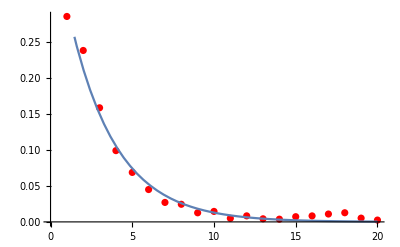

```mathematica
GraphicsGrid[{
ListPlot[#,Filling->Axis,PlotRange->All],
ListPlot[CorrelationFunction[#,{20}],Filling->Axis,PlotRange->All]
}&/@{arrivalintervals,serviceintervals,incrmntintervals,waitingintervals}//Transpose]
```

Effect of utility rate

Results from a queue with poisson arrival (λ=0.1) and exponential service (μ=1.5).

-Graphics-

Results from a queue with poisson arrival (λ=1.0) and exponential service (μ=1.5).

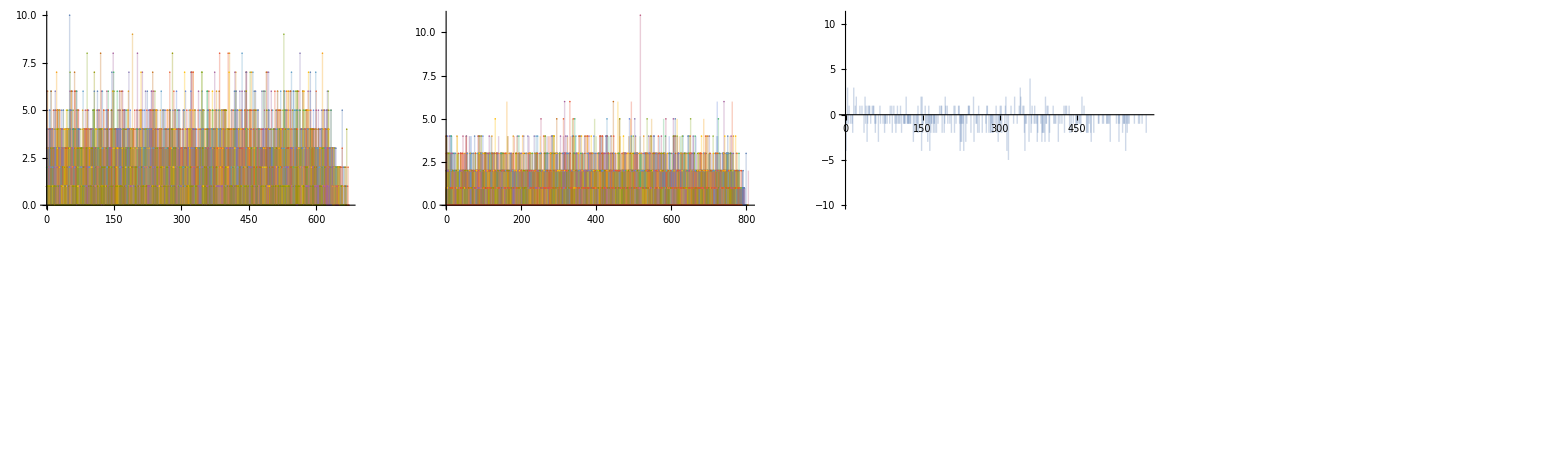

Results from a queue with poisson arrival (λ=1.45) and exponential service (μ=1.5).

-Graphics-

Effect of correlated increments

Results from a queue with poisson arrival (λ=1.0) and exponential service (μ=1.5).

-Graphics-

Results from a queue with auto-correlated arrival (λ≈1.0) and exponential service (μ=1.5).

-Graphics-

Note that waiting times are always strongly correlated; but the correlation of increments do increase that of the waiting times.

Show[{ListPlot[CorrelationFunction[waitingintervals,{20}],Filling→Axis,PlotRange→All,PlotStyle→Red],-Graphics-}]

-Graphics-

## New stuff